```mathematica
A = ({{-a1, 1}, {-a2, 0}});
Eigensystem[A]
```

{{1/2 (-a1-√(a1^2-4 a2)),1/2 (-a1+√(a1^2-4 a2))},{{-(-a1-√(a1^2-4 a2))/(2 a2),1},{-(-a1+√(a1^2-4 a2))/(2 a2),1}}}

```mathematica
w = ({{1/2 (-a1-√(a1^2-4 a2)), 0}, {0, 1/2 (-a1+√(a1^2-4 a2))}});
vr = ({{-(-a1-√(a1^2-4 a2))/(2 a2), -(-a1+√(a1^2-4 a2))/(2 a2)}, {1, 1}});
vrInv = Inverse[vr];
B =({{b1}, {b0}});
CMatrix = vrInv.B.Transpose[B].Transpose[vrInv];expw = ({{ⅇ^(1/2 (-a1-√(a1^2-4 a2))dt), 0}, {0, ⅇ^(1/2 (-a1+√(a1^2-4 a2))dt)}});
F = vr.expw.vrInv;
IntDT =∫_0^dt ({{ⅇ^(1/2 (-a1-√(a1^2-4 a2))x), 0}, {0, ⅇ^(1/2 (-a1+√(a1^2-4 a2))x)}}).CMatrix.({{ⅇ^(1/2 (-a1-√(a1^2-4 a2))x), 0}, {0, ⅇ^(1/2 (-a1+√(a1^2-4 a2))x)}})ⅆx;
IntInfinity =∫_0^∞ ({{ⅇ^(1/2 (-a1-√(a1^2-4 a2))x), 0}, {0, ⅇ^(1/2 (-a1+√(a1^2-4 a2))x)}}).CMatrix.({{ⅇ^(1/2 (-a1-√(a1^2-4 a2))x), 0}, {0, ⅇ^(1/2 (-a1+√(a1^2-4 a2))x)}})ⅆx;
Q = vr.IntDT.Transpose[vr];
Σ= vr.IntInfinity.Transpose[vr];
H = ({{1, 0}});
Cov = vr.expw.vrInv.Σ;
```

```mathematica
H.Cov.Transpose[H]
```

{{ConditionalExpression[(-1/(2 a2)(-a1+√(a1^2-4 a2)) (-((-a1+√(a1^2-4 a2)) ((a1+√(a1^2-4 a2)) b0-2 a2 b1)^2)/(8 (a1-√(a1^2-4 a2)) (a1^2-4 a2) a2)+((-a1-√(a1^2-4 a2)) (b0^2-a1 b0 b1+a2 b1^2))/(2 a1 (a1^2-4 a2)))-1/(2 a2)(-a1-√(a1^2-4 a2)) (-((-a1-√(a1^2-4 a2)) (-a1 b0+√(a1^2-4 a2) b0+2 a2 b1)^2)/(8 (a1+√(a1^2-4 a2)) (a1^2-4 a2) a2)+((-a1+√(a1^2-4 a2)) (b0^2-a1 b0 b1+a2 b1^2))/(2 a1 (a1^2-4 a2)))) (-((-a1-√(a1^2-4 a2)) ⅇ^(1/2 (-a1-√(a1^2-4 a2)) dt))/(2 √(a1^2-4 a2))+((-a1+√(a1^2-4 a2)) ⅇ^(1/2 (-a1+√(a1^2-4 a2)) dt))/(2 √(a1^2-4 a2)))+(-((-a1+√(a1^2-4 a2)) ((((a1+√(a1^2-4 a2)) b0-2 a2 b1)^2)/(4 (a1-√(a1^2-4 a2)) (a1^2-4 a2))-(a2 (b0^2-a1 b0 b1+a2 b1^2))/(a1 (a1^2-4 a2))))/(2 a2)-((-a1-√(a1^2-4 a2)) (((-a1 b0+√(a1^2-4 a2) b0+2 a2 b1)^2)/(4 (a1+√(a1^2-4 a2)) (a1^2-4 a2))-(a2 (b0^2-a1 b0 b1+a2 b1^2))/(a1 (a1^2-4 a2))))/(2 a2)) (-((-a1-√(a1^2-4 a2)) (-a1+√(a1^2-4 a2)) ⅇ^(1/2 (-a1-√(a1^2-4 a2)) dt))/(4 √(a1^2-4 a2) a2)+((-a1-√(a1^2-4 a2)) (-a1+√(a1^2-4 a2)) ⅇ^(1/2 (-a1+√(a1^2-4 a2)) dt))/(4 √(a1^2-4 a2) a2)),Re[a1]>0&&Re[a1]>Re[√(a1^2-4 a2)]&&Re[a1]>0&&Re[a1+√(a1^2-4 a2)]>0]}}

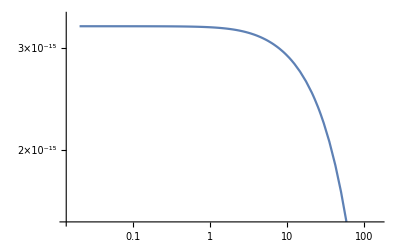

```mathematica
CovFunc[dt_,a1_,a2_,b0_,b1_]:=(-1/(2 a2)(-a1+√(a1^2-4 a2)) (-((-a1+√(a1^2-4 a2)) ((a1+√(a1^2-4 a2)) b0-2 a2 b1)^2)/(8 (a1-√(a1^2-4 a2)) (a1^2-4 a2) a2)+((-a1-√(a1^2-4 a2)) (b0^2-a1 b0 b1+a2 b1^2))/(2 a1 (a1^2-4 a2)))-1/(2 a2)(-a1-√(a1^2-4 a2)) (-((-a1-√(a1^2-4 a2)) (-a1 b0+√(a1^2-4 a2) b0+2 a2 b1)^2)/(8 (a1+√(a1^2-4 a2)) (a1^2-4 a2) a2)+((-a1+√(a1^2-4 a2)) (b0^2-a1 b0 b1+a2 b1^2))/(2 a1 (a1^2-4 a2)))) (-((-a1-√(a1^2-4 a2)) ⅇ^(1/2 (-a1-√(a1^2-4 a2)) dt))/(2 √(a1^2-4 a2))+((-a1+√(a1^2-4 a2)) ⅇ^(1/2 (-a1+√(a1^2-4 a2)) dt))/(2 √(a1^2-4 a2)))+(-((-a1+√(a1^2-4 a2)) ((((a1+√(a1^2-4 a2)) b0-2 a2 b1)^2)/(4 (a1-√(a1^2-4 a2)) (a1^2-4 a2))-(a2 (b0^2-a1 b0 b1+a2 b1^2))/(a1 (a1^2-4 a2))))/(2 a2)-((-a1-√(a1^2-4 a2)) (((-a1 b0+√(a1^2-4 a2) b0+2 a2 b1)^2)/(4 (a1+√(a1^2-4 a2)) (a1^2-4 a2))-(a2 (b0^2-a1 b0 b1+a2 b1^2))/(a1 (a1^2-4 a2))))/(2 a2)) (-((-a1-√(a1^2-4 a2)) (-a1+√(a1^2-4 a2)) ⅇ^(1/2 (-a1-√(a1^2-4 a2)) dt))/(4 √(a1^2-4 a2) a2)+((-a1-√(a1^2-4 a2)) (-a1+√(a1^2-4 a2)) ⅇ^(1/2 (-a1+√(a1^2-4 a2)) dt))/(4 √(a1^2-4 a2) a2));
LogLogPlot[CovFunc[dt,0.75,0.01,7.0*10^-9,1.2*10^-9],{dt,0.02,100}]
```